### Base

Set the Census API key

```mathematica
(*SystemCredential["USCensusAPIKey"]="your Census API key"*)
```

```mathematica
Options[censusQuery]={
Authentication:>SystemCredential["USCensusAPIKey"],
"APIBase"->"api.census.gov"
};
```

```mathematica
censusQuery[path_,query_,opts:OptionsPattern[]]:=
Enclose@Module[{rawResponse,responseList},
rawResponse=Confirm@URLRead@HTTPRequest[<|
"Scheme"->"HTTPS",
"Domain"->OptionValue["APIBase"],
"Path"->path,
"Query"->Join[
query,
{"key"->OptionValue[Authentication]}
]
|>];
responseList=Confirm@Import[rawResponse,"RawJSON"];
ToTabular[Rest@responseList,"Rows",<|"ColumnKeys"->First@responseList|>]
]
```

Get tract-level estimates for a variable:

```mathematica
tractValues[vars_,fipsCode_,path_]:=
Module[{tab},
tab=censusQuery[
path,
{
"get"->StringRiffle[vars,","],
"for"->"tract:*",
"in"->"state:"<>fipsCode,
"in"->"county:*"
}
];
tab=ConstructColumns[tab,
{
"geoid"->Function[#state<>#county<>#tract],
"total"->Function[Total@ToExpression@Lookup[#,vars]]
}
];
GroupBy[FromTabular[tab,"Rows"],Lookup["geoid"]->Lookup["total"],First]
]
```

```mathematica
allStateValues[vars_,path_]:=
Module[{tab},
tab=censusQuery[
path,
{
"get"->StringRiffle[vars,","],
"for"->"state:*"
}
];
tab=ConstructColumns[tab,
{
"geoid"->Function[#state],
"total"->Function[Total@ToExpression@Lookup[#,vars]]
}
];
GroupBy[FromTabular[tab,"Rows"],Lookup["geoid"]->Lookup["total"],First]
]
```

### Comparison

We compute the number of Hispanic White alone people in each tract in Georgia using data from the 5 year ACS (2022 vintage) and the 2020 Decennial Census.

For each, we first get the number of White alone people using the following variables:

ACS: B01001A_001E ("Estimate!!Total:" from "Sex by Age (White Alone)")

Decennial Census: P1_003N ("!!Total:!!Population of one race:!!White alone")

We then get the number of non-Hispanic White alone people using the following variables:

ACS: B01001H_001E ("Estimate!!Total:" from "Sex by Age (White Alone, Not Hispanic or Latino)")

Decennial Census: P2_005N ("!!Total:!!Not Hispanic or Latino:!!Population of one race:!!White alone")

Compute the estimates:

```mathematica
pathACS={"data","2022","acs","acs5"};
```

```mathematica
pathACS={"data","2022","acs","acs5"};
pathDec={"data","2020","dec","pl"};
```

```mathematica
fipsCode=Entity["AdministrativeDivision",{"Georgia","UnitedStates"}][EntityProperty["AdministrativeDivision","FIPSCode"]]
```

13

```mathematica
tractCountsACS=
tractValues[{"B01001A_001E"},fipsCode,pathACS]-
tractValues[{"B01001H_001E"},fipsCode,pathACS];
tractCountsDec=
tractValues[{"P1_003N"},fipsCode,pathDec]-
tractValues[{"P2_005N"},fipsCode,pathDec];
```

The results are very different from the ACS and Decennial Census:

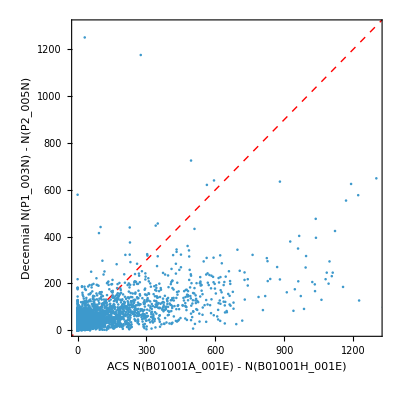

```mathematica
ListPlot[
Values@Merge[{tractCountsACS,tractCountsDec},Identity],
Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]},
AspectRatio->Automatic,
PlotRange->{{0,1300},{0,1300}},
Frame->True,
FrameLabel->{"ACS N(B01001A_001E) - N(B01001H_001E)","Decennial N(P1_003N) - N(P2_005N)"}
]
```

Their distributions are different too. The ACS has far more zero inflation, but also has a fatter tail:

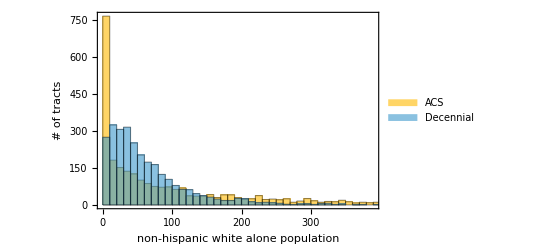

```mathematica
Histogram[{
tractCountsACS,
tractCountsDec
},
{10},
ChartLegends->{"ACS","Decennial"},
Frame->True,FrameLabel->{"non-hispanic white alone population","# of tracts"}
]
```

Comparing the direct variables from the ACS and Decennial Census on their own, they don't look too dissimilar:

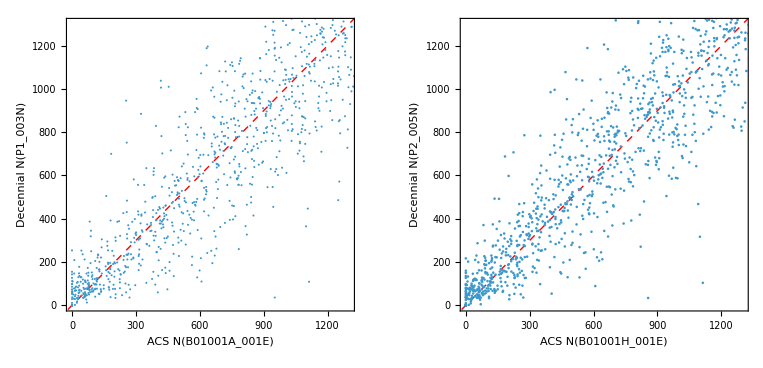

```mathematica
GraphicsRow[{
ListPlot[
Values@Merge[{
tractValues[{"B01001A_001E"},fipsCode,pathACS],
tractValues[{"P1_003N"},fipsCode,pathDec]
},Identity],
Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]},
AspectRatio->Automatic,
PlotRange->{{0,1300},{0,1300}},
Frame->True,
FrameLabel->{"ACS N(B01001A_001E)","Decennial N(P1_003N)"}
],
ListPlot[
Values@Merge[{
tractValues[{"B01001H_001E"},fipsCode,pathACS],
tractValues[{"P2_005N"},fipsCode,pathDec]
},Identity],
Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]},
AspectRatio->Automatic,
PlotRange->{{0,1300},{0,1300}},
Frame->True,
FrameLabel->{"ACS N(B01001H_001E)","Decennial N(P2_005N)"}
]
}]
```

### Statewide

The state-level numbers also disagree:

```mathematica
stateValue[vars_,fipsCode_,path_]:=Total@ToExpression@Normal@censusQuery[path,{"get"->StringRiffle[vars,","],"for"->"state:"<>fipsCode}][[1,vars]]
```

ACS value:

```mathematica
stateValue[{"B01001A_001E"},fipsCode,pathACS]-
stateValue[{"B01001H_001E"},fipsCode,pathACS]
```

374864

Decennial value:

```mathematica
stateValue[{"P1_003N"},fipsCode,pathDec]-
stateValue[{"P2_005N"},fipsCode,pathDec]
```

193327

### Links

https://data.census.gov/table?q=ACSDT5Y2022.B01001A&g=040XX00US13
https://data.census.gov/table?q=ACSDT5Y2022.B01001H&g=040XX00US13

https://data.census.gov/table/DECENNIALPL2020.P1?q=P1&g=040XX00US13
https://data.census.gov/table/DECENNIALPL2020.P2?q=P2&g=040XX00US13

### State-level

```mathematica
pathACS={"data","2022","acs","acs5"};
```

```mathematica
stateCountsACS=
allStateValues[{"B01001A_001E"},pathACS]-
allStateValues[{"B01001H_001E"},pathACS];
stateCountsDec=
allStateValues[{"P1_003N"},pathDec]-
allStateValues[{"P2_005N"},pathDec];
```

```mathematica
fipsStates=AssociationMap[Reverse,EntityValue[EntityClass["AdministrativeDivision","AllUSStatesPlusDC"],"FIPSCode","EntityAssociation"]];
```

```mathematica
ListPlot[
KeyMap[fipsStates,Merge[{stateCountsACS,stateCountsDec},Identity]],
Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]},
AspectRatio->Automatic,
(*PlotRange->{{0,1300},{0,1300}},*)
Frame->True,
FrameLabel->{"ACS N(B01001A_001E) - N(B01001H_001E)","Decennial N(P1_003N) - N(P2_005N)"}
]
```

-Graphics-

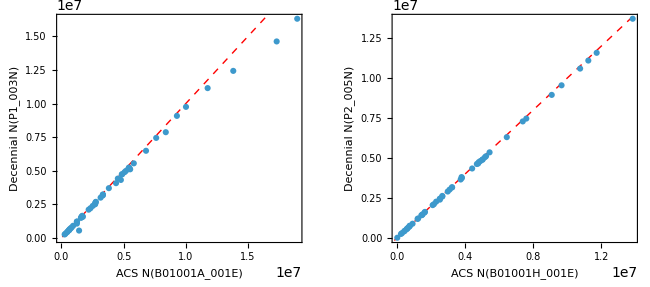

```mathematica
GraphicsRow[{
ListPlot[
Values@Merge[{
allStateValues[{"B01001A_001E"},pathACS],
allStateValues[{"P1_003N"},pathDec]
},Identity],
Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]},
AspectRatio->Automatic,
PlotRange->All,
Frame->True,
FrameLabel->{"ACS N(B01001A_001E)","Decennial N(P1_003N)"}
],
ListPlot[
Values@Merge[{
allStateValues[{"B01001H_001E"},pathACS],
allStateValues[{"P2_005N"},pathDec]
},Identity],
Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]},
AspectRatio->Automatic,
PlotRange->All,
Frame->True,
FrameLabel->{"ACS N(B01001H_001E)","Decennial N(P2_005N)"}
]
}]
```

### Different vintages

#### 2022 1-year

```mathematica
pathACS={"data","2022","acs","acs1"};
```

```mathematica
stateCountsACS=
allStateValues[{"B01001A_001E"},pathACS]-
allStateValues[{"B01001H_001E"},pathACS];
stateCountsDec=
allStateValues[{"P1_003N"},pathDec]-
allStateValues[{"P2_005N"},pathDec];
```

```mathematica
ListPlot[
KeyMap[fipsStates,Merge[{stateCountsACS,stateCountsDec},Identity]],
Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]},
AspectRatio->Automatic,
(*PlotRange->{{0,1300},{0,1300}},*)
Frame->True,
FrameLabel->{"ACS N(B01001A_001E) - N(B01001H_001E)","Decennial N(P1_003N) - N(P2_005N)"}
]
```

-Graphics-

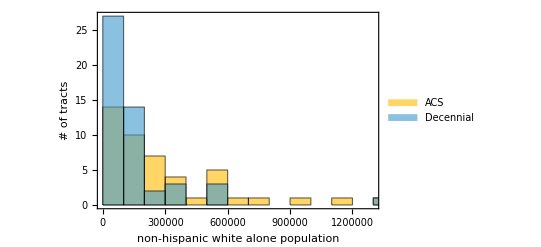

```mathematica
Histogram[{
stateCountsACS,
stateCountsDec
},
{100000},
ChartLegends->{"ACS","Decennial"},
Frame->True,FrameLabel->{"non-hispanic white alone population","# of tracts"}
]
```

#### 2019 1-year

```mathematica
pathACS={"data","2019","acs","acs1"};
```

```mathematica
stateCountsACS=
allStateValues[{"B01001A_001E"},pathACS]-
allStateValues[{"B01001H_001E"},pathACS];
stateCountsDec=
allStateValues[{"P1_003N"},pathDec]-
allStateValues[{"P2_005N"},pathDec];
```

```mathematica
ListPlot[
KeyMap[fipsStates,Merge[{stateCountsACS,stateCountsDec},Identity]],
Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]},
AspectRatio->Automatic,
(*PlotRange->{{0,1300},{0,1300}},*)
Frame->True,
FrameLabel->{"ACS N(B01001A_001E) - N(B01001H_001E)","Decennial N(P1_003N) - N(P2_005N)"}
]
```

-Graphics-

### Slope over time

```mathematica
getScatterPoints[year_]:=Module[{pathACS,stateCountsACS,stateCountsDec},
pathACS={"data",ToString[year],"acs","acs1"};
stateCountsACS=
allStateValues[{"B01001A_001E"},pathACS]-
allStateValues[{"B01001H_001E"},pathACS];
stateCountsDec=
allStateValues[{"P1_003N"},pathDec]-
allStateValues[{"P2_005N"},pathDec];
KeyMap[fipsStates,Merge[{stateCountsACS,stateCountsDec},Identity]]
]
```

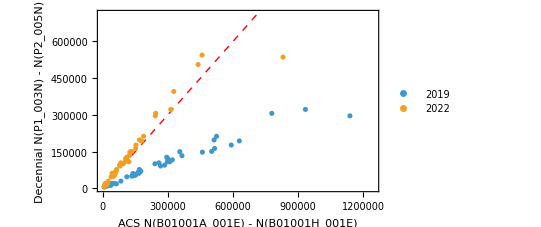

```mathematica
ListPlot[
Values/@{getScatterPoints[2019],getScatterPoints[2022]},
Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]},
AspectRatio->Automatic,
(*PlotRange->{{0,1300},{0,1300}},*)
Frame->True,
FrameLabel->{"ACS N(B01001A_001E) - N(B01001H_001E)","Decennial N(P1_003N) - N(P2_005N)"},
PlotLegends->Placed[{2019,2022},{Right,Top}]
]
```

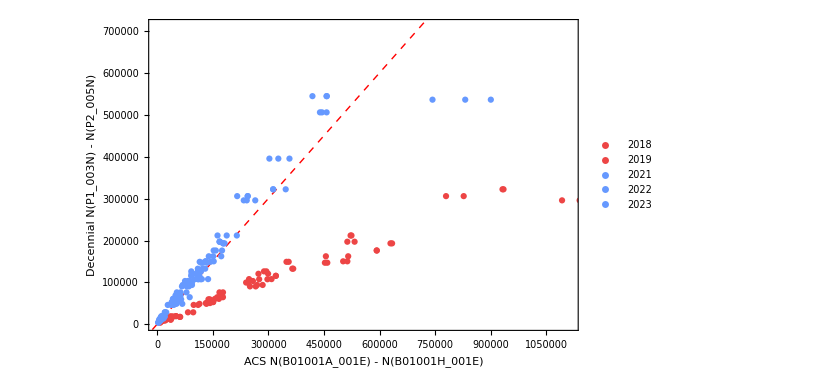

```mathematica
With[{years={2018,2019,2021,2022,2023}},
ListPlot[
Function[y,KeyValueMap[Function[{state,p},Tooltip[p,{state,y}]],getScatterPoints[y]]]/@years,
Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]},
AspectRatio->Automatic,
(*PlotRange->{{0,1300},{0,1300}},*)
Frame->True,
FrameLabel->{"ACS N(B01001A_001E) - N(B01001H_001E)","Decennial N(P1_003N) - N(P2_005N)"},
PlotLegends->Placed[years,{Right,Top}],
PlotStyle->(If[#>=2020,StandardBlue,StandardRed]&/@years)
]
]
```

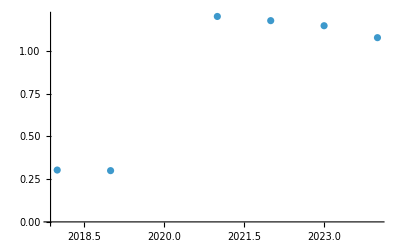

```mathematica
With[{years={2018,2019,2021,2022,2023,2024}},
ListPlot@Transpose[{
years,
LinearModelFit[Values@getScatterPoints[#],x,x]["BestFitParameters"][[2]]&/@years
}]
]
```

## Old versions

### ACS

From https://api.census.gov/data/2023/acs/acs5/variables.html

```mathematica
(*allWhiteVarsACS={"B05003A_001E"};
nonHispanicWhiteVarsACS={"B05003H_001E"};*)
```

ACS: B05003A_001E ("Estimate!!Total:" from "Sex by Age by Nativity and Citizenship Status (White Alone)")

ACS: B05003H_001E ("Estimate!!Total:" from "Sex by Age by Nativity and Citizenship Status (White Alone, Not Hispanic or Latino)")

```mathematica
allWhiteVarsACS={"B01001A_001E"};
nonHispanicWhiteVarsACS={"B01001H_001E"};
```

ACS: B01001A_001E ("Estimate!!Total:" from "Sex by Age (White Alone)")

ACS: B01001H_001E ("Estimate!!Total:" from "Sex by Age (White Alone, Not Hispanic or Latino)")

```mathematica
acsTab=censusQuery[
{"data","2022","acs","acs5"},
{
"get"->StringRiffle[Join[allWhiteVarsACS,nonHispanicWhiteVarsACS],","],
"for"->"tract:*",
"in"->"state:"<>fipsCode,
"in"->"county:*"
}
]
```

```mathematica
hispanicWhiteTabACS=ConstructColumns[acsTab,
{
"geoid"->Function[#state<>#county<>#tract],
"hispanic_white"->Function[
Total@ToExpression@Lookup[#,allWhiteVarsACS]-
Total@ToExpression@Lookup[#,nonHispanicWhiteVarsACS]
]
}
]
```

```mathematica
hispanicWhiteCountsACS=GroupBy[FromTabular[hispanicWhiteTabACS,"Rows"],Lookup["geoid"]->Lookup["hispanic_white"],First];
```

### Decennial

From https://api.census.gov/data/2020/dec/pl/variables.html

```mathematica
allWhiteVarsDec={"P1_003N"};
nonHispanicWhiteVarsDec={"P2_005N"};
```

```mathematica
decTab=censusQuery[
{"data","2020","dec","pl"},
{
"get"->StringRiffle[Join[allWhiteVarsDec,nonHispanicWhiteVarsDec],","],
"for"->"tract:*",
"in"->"state:"<>fipsCode,
"in"->"county:*"
}
]
```

```mathematica
hispanicWhiteTabDec=ConstructColumns[decTab,
{
"geoid"->Function[#state<>#county<>#tract],
"hispanic_white"->Function[
Total@ToExpression@Lookup[#,allWhiteVarsDec]-
Total@ToExpression@Lookup[#,nonHispanicWhiteVarsDec]
]
}
]
```

```mathematica
hispanicWhiteCountsDec=GroupBy[FromTabular[hispanicWhiteTabDec,"Rows"],Lookup["geoid"]->Lookup["hispanic_white"],First];
```